I want to understand how to solve a partially reduced Sylvester equation from

Golub, G.; Nash, S.; Loan, C. Van (1979). “A Hessenberg–Schur method for the problem AX + XB= C”. IEEE Transactions on Automatic Control. 24 (6): 909–913. doi:10.1109/TAC.1979.1102170. hdl:1813/7472. ISSN 0018-9286.

@ARTICLE{1102170,
  author={Golub, G. and Nash, S. and Van Loan, C.},
  journal={IEEE Transactions on Automatic Control}, 
  title={A Hessenberg-Schur method for the problem AX + XB= C}, 
  year={1979},
  volume={24},
  number={6},
  pages={909-913},
  doi={10.1109/TAC.1979.1102170}}

1.04634×10^-14

9.96389×10^-15

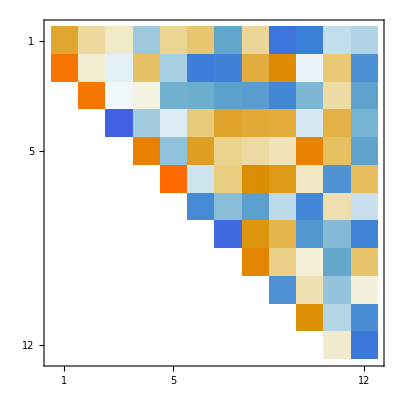
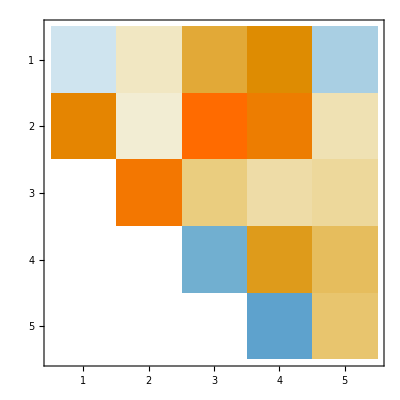

```mathematica
{m,n}={12,5};
{A,B,X}=Map[RandomReal[{-1,1},#]&,{{m,m},{n,n},{m,n}}];
RHS=A.X+X.B;
Norm[X-LyapunovSolve[A,B,RHS]]
{{QA,HA},{QB,HB}}=Map[HessenbergDecomposition,{A,B}];
Map[Norm,{A-QA.HA.QAᵀ,B-QB.HB.QBᵀ}];
(* Solved Reduced Equation *)
Norm[X-QA.LyapunovSolve[HA,HB,QAᵀ.RHS.QB].QBᵀ]
Map[MatrixPlot,{HA,HB}]
```

### Triangular Back Solve

If T x=b with T triangular then the last (bottom) equation is 
	T_(m,m)x_m=b_m⟺x_m=b_m/(T_(m,m))
and the second last is 
	T_(m-1,m-1)x_(m-1)+T_(m-1,m)x_(m-1)=b_(m-1)⟺x_(m-1)=1/(T_(m-1,m-1))(b_(m-1)-T_(m-1,m)x_m)
which can be evaluated sequentially.

```mathematica
BackSubT[T_,b_]:=Module[{x=0.0*b,m=Length[b]},
Do[
x⟦i⟧=1/T⟦i,i⟧(b⟦i⟧-Sum[T⟦i,j⟧ x⟦j⟧,{j,i+1,m}]),
{i,m,1,-1}];
x
]
```

Testing

```mathematica
m=126;
x=RandomReal[{-1,1},m];
T=UpperTriangularize[RandomReal[{-1,1},{m,m}]]+20IdentityMatrix[m];
b=T.x;
xMma=LinearSolve[T,b];
xT = BackSubT[T,b];
Map[Norm,{x-xMma,x-xT,xMma-xT}]
```

{3.1105×10^-15,1.39906×10^-15,3.23296×10^-15}

### Hessenberg Back Solve

A Hessenberg BackSolve (I know I saw this somewhere).  Assign a symbolic value to the last entry and solve with that symbolic value in place.

If H x=b with H upper Hessenberg then the last (bottom) equation is 
	H_(m,m)x_m+H_(m,m-1)x_(m-1)=b_m⟺x_(m-1)=b_m/(H_(m,m-1))-(H_(m,m))/(H_(m,m-1))x_m
and the second last is 
	H_(m-1,m)x_m+H_(m-1,m-1)x_(m-1)+H_(m-1,m-2)x_(m-2)=b_(m-1)⟺x_(m-2)=(b_(m-1))/(H_(m-1,m-2))-(H_(m-1,m))/(H_(m,m-2))x_m-(H_(m-1,m-1))/(H_(m,m-2))x_(m-1)
which can be evaluated sequentially.

```mathematica
m=11;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
xNew=0*x;
Clear[γ]
xNew⟦m⟧=γ;
xNew⟦m-1⟧=Expand[1/H⟦m,m-1⟧(b⟦m⟧-H⟦m,m⟧xNew⟦m⟧)];
xNew⟦m-2⟧=Expand[1/H⟦m-1,m-2⟧(b⟦m-1⟧-H⟦m-1,m⟧xNew⟦m⟧-H⟦m-1,m-1⟧xNew⟦m-1⟧)];
xNew⟦m-3⟧=Expand[1/H⟦m-2,m-3⟧(b⟦m-2⟧-H⟦m-2,m⟧xNew⟦m⟧-H⟦m-2,m-1⟧xNew⟦m-1⟧-H⟦m-2,m-2⟧xNew⟦m-2⟧)];
xNew⟦m-4⟧=Expand[1/H⟦m-3,m-4⟧(b⟦m-3⟧-H⟦m-3,m⟧xNew⟦m⟧-H⟦m-3,m-1⟧xNew⟦m-1⟧-H⟦m-3,m-2⟧xNew⟦m-2⟧-H⟦m-3,m-3⟧xNew⟦m-3⟧)];
xNew⟦-5;;-1⟧/.γ->x⟦-1⟧
x⟦-5;;-1⟧
```

{0.936329,-0.438589,0.182932,-0.751584,0.394746}

{0.936329,-0.438589,0.182932,-0.751584,0.394746}

```mathematica
BackSubH[H_,b_]:=Module[{x=0.0*{b,b}ᵀ,m=Length[b]},
x⟦m⟧={0,1};
Do[
x⟦i-1⟧=1/H⟦i,i-1⟧({b⟦i⟧,0}-Sum[{H⟦i,j⟧,0} x⟦j⟧,{j,i,m}]),
{i,m,2,-1}];
x
]
```

```mathematica
m=11;
H=UpperTriangularize[RandomReal[{-1,1},{m,m}],-1];
x=RandomReal[{-1,1},m];
b=H.x;
Clear[γ]
xMma=LinearSolve[H,b]
{c0,cγ}=BackSubH[H,b]ᵀ;
c0+x⟦-1⟧ cγ
```

{-0.604442,0.961181,-0.261392,0.712874,0.481596,-0.762879,-0.680206,0.567236,0.797035,-0.0787393,0.833621}

{351.634,-35.3615,-45.2763,31.1588,7.45093,7.54716,-8.19038,-1.46612,7.75033,-1.84776,0.833621}